## Test on Molecules

## Initialize

### Load images

```mathematica
validationRoot="/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated";
validationImages="images";
validationResult="molfiles";
validationDumps="dumps";
```

```mathematica
<<"/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Drafts/ChemicalLines.wl"
```

```mathematica
SetDirectory["/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Outputs"];
```

```mathematica
images=Import[FileNameJoin[{validationRoot,validationDumps,"images.mx"}]];
```

## Set up for outputing graphs

```mathematica
SetDirectory["/Users/Corwin/projects/WolframSummerSchool/presentationOutputs/MoleculeAndGraph"]
```

/Users/Corwin/projects/WolframSummerSchool/presentationOutputs/MoleculeAndGraph

## Run 1

### Image

```mathematica
i=images[[1493]]
```

-Graphics-

```mathematica
lineSize=30;
mergeThreshold=42;
```

### Lines

```mathematica
allLines=doLineDetect[i,0.05,0.01];
showLines[i,allLines]
```

-Graphics-

```mathematica
longLines=pickLongLines[allLines,lineSize];
showLines[i,longLines]
```

-Graphics-

#### Parallel lines

```mathematica
degreeTolerance=10;
parallelLongLinesByAngle=Gather[Sort[longLines],Not[degreeTolerance<Abs[lineAngle[#1]/Degree-lineAngle[#2]/Degree]<(180-degreeTolerance)]&];
```

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,parallelLongLinesByAngle[[n]]],ImageSize->Small],{n,1,Length[parallelLongLinesByAngle],1}]
```

#### Nearby lines

```mathematica
nearbyParallelLinesByAngle=Map[gatherNearbyLinesByCenter[#,80]&,parallelLongLinesByAngle];
```

```mathematica
Manipulate[HighlightImage[i,nearbyParallelLinesByAngle[[n,m]],ImageSize->Small],{{m,1,"Close Set"},1,10,1},{{n,1,"Parallel Set"},1,Length@nearbyParallelLinesByAngle,1}]
```

#### Intersecting Lines

```mathematica
intersectingNearbyParallelLinesByAngle=Map[gatherIntersectingLines,nearbyParallelLinesByAngle,{2}];
```

#### Merge intersecting lines

```mathematica
singlesA=Cases[intersectingNearbyParallelLinesByAngle,{_Line},{4}];
```

```mathematica
mergeA1=Cases[intersectingNearbyParallelLinesByAngle,{{Repeated[_Line,{2}]}..},{3}];
```

```mathematica
mergeA2Prelim=Cases[intersectingNearbyParallelLinesByAngle,{Repeated[{Repeated[_Line,{2}]},{1,Infinity}],Repeated[{_Line},{1,Infinity}]},{3}];
```

```mathematica
mergeA2=DeleteCases[mergeA2Prelim,{_Line},{2}];
```

```mathematica
mergeA=Join[mergeA1,mergeA2];
```

```mathematica
mergedIntersectingNearbyParallelLinesByAngle= Map[mergeLines,mergeA,{1}];
```

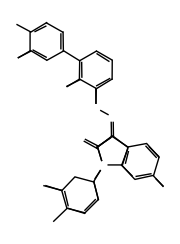

```mathematica
cleanLines=Flatten@Join[singlesA,mergedIntersectingNearbyParallelLinesByAngle];
Graphics[cleanLines,ImageSize->Small]
```

### Vertices

```mathematica
cleanPoints=Sort@Flatten[First/@cleanLines,1];
```

```mathematica
Manipulate[Graphics[{Thin,Gray,cleanLines,Black,Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<t&]]]},ImageSize->Medium],{t,1,100}]
```

```mathematica
mergedPoints=Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<mergeThreshold&]]];
```

```mathematica
cleanPointsGathered=Gather[cleanPoints,EuclideanDistance[#1,#2]<mergeThreshold&];
```

```mathematica
mergedPoints=Point/@Mean/@cleanPointsGathered;
```

```mathematica
mergedPointParents=AssociationThread[mergedPoints,Map[Point,cleanPointsGathered,{2}]];
```

```mathematica
separatePointsChild=Merge[Flatten@Map[Reverse,Thread/@Normal[mergedPointParents],{2}],Identity];
```

#### Tracing Vertices

```mathematica
edgeListTargets=Map[traceConnections[#,cleanLines,mergedPoints,mergedPointParents,separatePointsChild]&,mergedPoints]
```

{{4},{3,3},{4,7,2,2,7},{3,6,1,6},{11,11},{10,4,4},{9,3,3},{12},{10,16,10,7},{9,9,6},{12,14,5,5,12},{18,11,8,18,11},{15,15},{19,11},{20,16,13,13,16},{22,15,9,15},{24,24},{21,21,12,12},{25,21,21,19,19,21,21,19,19,14,25},{23,23,28,28,23,23,15},{18,19,19,21,21,19,19,21,21,18},{27,27,16},{20,23,23,20,23,23,26},{29,29,29,25,25,24,24,25,25,24,24,17,17},{19,19,24,24,25,25,24,24,25,25,30},{23,29,29},{22,28,22},{20,27,20},{24,31,26,24,31,26,24},{32,32,31,31,25,31},{33,29,30,30,29,30},{30,34,30,34},{35,35,31,35},{32,36,35,32,36},{33,34,33,33},{34,34}}

```mathematica
edgePairs=Thread/@Transpose[{Range[Length[edgeListTargets]],edgeListTargets}]
```

{{{1,4}},{{2,3},{2,3}},{{3,4},{3,7},{3,2},{3,2},{3,7}},{{4,3},{4,6},{4,1},{4,6}},{{5,11},{5,11}},{{6,10},{6,4},{6,4}},{{7,9},{7,3},{7,3}},{{8,12}},{{9,10},{9,16},{9,10},{9,7}},{{10,9},{10,9},{10,6}},{{11,12},{11,14},{11,5},{11,5},{11,12}},{{12,18},{12,11},{12,8},{12,18},{12,11}},{{13,15},{13,15}},{{14,19},{14,11}},{{15,20},{15,16},{15,13},{15,13},{15,16}},{{16,22},{16,15},{16,9},{16,15}},{{17,24},{17,24}},{{18,21},{18,21},{18,12},{18,12}},{{19,25},{19,21},{19,21},{19,19},{19,19},{19,21},{19,21},{19,19},{19,19},{19,14},{19,25}},{{20,23},{20,23},{20,28},{20,28},{20,23},{20,23},{20,15}},{{21,18},{21,19},{21,19},{21,21},{21,21},{21,19},{21,19},{21,21},{21,21},{21,18}},{{22,27},{22,27},{22,16}},{{23,20},{23,23},{23,23},{23,20},{23,23},{23,23},{23,26}},{{24,29},{24,29},{24,29},{24,25},{24,25},{24,24},{24,24},{24,25},{24,25},{24,24},{24,24},{24,17},{24,17}},{{25,19},{25,19},{25,24},{25,24},{25,25},{25,25},{25,24},{25,24},{25,25},{25,25},{25,30}},{{26,23},{26,29},{26,29}},{{27,22},{27,28},{27,22}},{{28,20},{28,27},{28,20}},{{29,24},{29,31},{29,26},{29,24},{29,31},{29,26},{29,24}},{{30,32},{30,32},{30,31},{30,31},{30,25},{30,31}},{{31,33},{31,29},{31,30},{31,30},{31,29},{31,30}},{{32,30},{32,34},{32,30},{32,34}},{{33,35},{33,35},{33,31},{33,35}},{{34,32},{34,36},{34,35},{34,32},{34,36}},{{35,33},{35,34},{35,33},{35,33}},{{36,34},{36,34}}}

```mathematica
edgeList=Flatten@Map[UndirectedEdge@@#&,edgePairs,{2}]
```

{1<->4,2<->3,2<->3,3<->4,3<->7,3<->2,3<->2,3<->7,4<->3,4<->6,4<->1,4<->6,5<->11,5<->11,6<->10,6<->4,6<->4,7<->9,7<->3,7<->3,8<->12,9<->10,9<->16,9<->10,9<->7,10<->9,10<->9,10<->6,11<->12,11<->14,11<->5,11<->5,11<->12,12<->18,12<->11,12<->8,12<->18,12<->11,13<->15,13<->15,14<->19,14<->11,15<->20,15<->16,15<->13,15<->13,15<->16,16<->22,16<->15,16<->9,16<->15,17<->24,17<->24,18<->21,18<->21,18<->12,18<->12,19<->25,19<->21,19<->21,19<->19,19<->19,19<->21,19<->21,19<->19,19<->19,19<->14,19<->25,20<->23,20<->23,20<->28,20<->28,20<->23,20<->23,20<->15,21<->18,21<->19,21<->19,21<->21,21<->21,21<->19,21<->19,21<->21,21<->21,21<->18,22<->27,22<->27,22<->16,23<->20,23<->23,23<->23,23<->20,23<->23,23<->23,23<->26,24<->29,24<->29,24<->29,24<->25,24<->25,24<->24,24<->24,24<->25,24<->25,24<->24,24<->24,24<->17,24<->17,25<->19,25<->19,25<->24,25<->24,25<->25,25<->25,25<->24,25<->24,25<->25,25<->25,25<->30,26<->23,26<->29,26<->29,27<->22,27<->28,27<->22,28<->20,28<->27,28<->20,29<->24,29<->31,29<->26,29<->24,29<->31,29<->26,29<->24,30<->32,30<->32,30<->31,30<->31,30<->25,30<->31,31<->33,31<->29,31<->30,31<->30,31<->29,31<->30,32<->30,32<->34,32<->30,32<->34,33<->35,33<->35,33<->31,33<->35,34<->32,34<->36,34<->35,34<->32,34<->36,35<->33,35<->34,35<->33,35<->33,36<->34,36<->34}

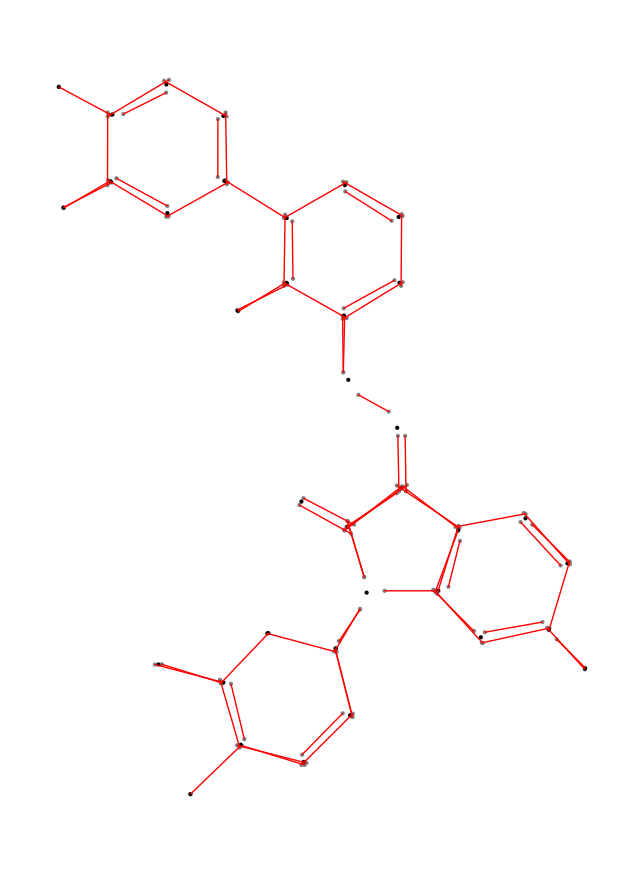

```mathematica
Graphics[{Gray,Point/@cleanPoints,Thick,Black,mergedPoints,Thin,Red,cleanLines}]
```

```mathematica
directedEdgeList=Flatten@Map[DirectedEdge@@#&,edgePairs,{2}];
```

```mathematica
graphOfMolecule=Graph[Range[Length[mergedPoints]],directedEdgeList]
```

-Graphics-

```mathematica
{i,Show[graphOfMolecule,AspectRatio->1/GoldenRatio]}
```

{-Graphics-,-Graphics-}

```mathematica
graphPic=Rasterize[graphOfMolecule,ImageResolution->200]
```

-Graphics-

```mathematica
noDuplicateEdgePairs=DeleteDuplicates[Sort/@Flatten[edgePairs,1]];
```

```mathematica
noSelfBond=DeleteCases[noDuplicateEdgePairs,{ee_,ee_}];
```

```mathematica
undirectedEdgeList=Map[UndirectedEdge@@#&,noSelfBond,{1}];
```

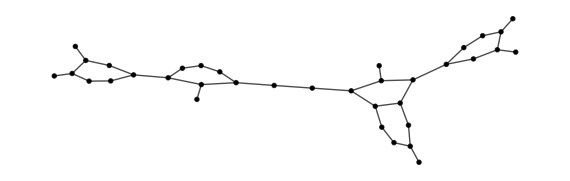

```mathematica
Graph[Range[Length[mergedPoints]],undirectedEdgeList,EdgeStyle->Black,VertexStyle->Black]
```

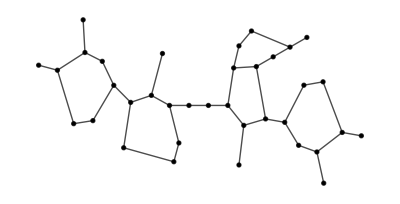

```mathematica
Graph[Range[Length[mergedPoints]],undirectedEdgeList,EdgeStyle->Black,VertexStyle->Black,GraphLayout->"RadialEmbedding"]
```

### Recognize Text

### Molecule

```mathematica
atomList=Table["C",Length[mergedPoints]]
```

{C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C}

```mathematica
noDuplicateEdgePairs=DeleteDuplicates[Sort/@Flatten[edgePairs,1]];
```

```mathematica
noSelfBond=DeleteCases[noDuplicateEdgePairs,{ee_,ee_}];
```

```mathematica
bondList=Apply[Bond@*List,noSelfBond,2];
```

```mathematica
molecule=Molecule[atomList,bondList]
```

Molecule[…]